Dirac Cones in electronic and magnetic systems 
This notebook will investigate Dirac cones in 2d Van der Waals systems starting with the electronic system of graphene then considering the magnetic analogue, the honeycomb ferromagnet. We will then explore the survival of the Dirac cones with different stacking configurations to see if any Dirac cones survive and other features of the band structure that arise. This will give us an insight into how the coupling may vary over the moire unit cell which will have lots of different coupling configurations which vary slowly across the cell.

### Line Plots

We will produce both 3D plots and line plots between high symmetry points in the honeycomb systems. These are the centre of the hexagon the Dirac point on lattice A and the Dirac point on lattice B .

```mathematica
F=(2*Pi)/(3*Sqrt[3]*a);
ky1=Function[{kx},0];
ky2=Function[{kx},-Sqrt[3]*(kx-2*F)];
ky3= Function[{kx},Sqrt[3]* (kx)];
kx1=Function[kx,kx];
kx2=Function[kx,-kx+F];
kx3=Function[kx,-kx+4 F];

LinePlot= Function[{E1,E2,E3,a,b,c,d,kx},Piecewise[{{E1,a<=kx<=b},{E2,b<=kx<=c},{E3,c<=kx<=d}}]];

gamsq=Function[{a,kx,ky},3+4 Cos[(Sqrt[3]/2 )*kx *a] Cos[(3/2 )*ky* a]+2 Cos[Sqrt[3]kx a]];

t=1;
a=1;
JHS=1;
LF=-0.3;
LA=0.3;
```

## Graphene

3D plot

```mathematica
Ek=Function[{t,a,kx,ky},t* Sqrt[gamsq[a,kx,ky]]];
Plot3D[{Ek[t,a,kx,ky],Ek[-t,a,kx,ky]}, {kx, -4,4},{ky,-4,4}, AxesLabel->{kx,ky,"E(k)"}]
```

-Graphics3D-

Line plots

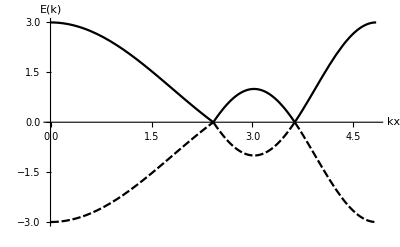

```mathematica
Plot[{LinePlot[Ek[t,a,kx1[kx],ky1[kx1[kx]]],Ek[t,a,kx2[kx],ky2[kx2[kx]]],Ek[t,a,kx3[kx],ky3[kx3[kx]]],0,2*F,3*F,4*F,kx],LinePlot[Ek[-t,a,kx1[kx],ky1[kx1[kx]]],Ek[-t,a,kx2[kx],ky2[kx2[kx]]],Ek[-t,a,kx3[kx],ky3[kx3[kx]]],0,2*F,3*F,4*F,kx],PlotStyle->Dashed},{kx,0,4*F},GridLines->{{2*F,3*F,4*F},{0}},AxesLabel->{kx,"E(k)"},PlotTheme->"Monochrome"]
```

Plot along (1, 1, 0 ) to compare with spin w

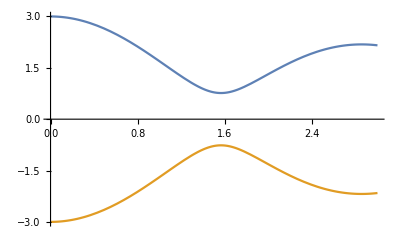

```mathematica
Plot[{Ek[t,a,kx,kx],Ek[-t,a,kx,kx]},{kx,0,3}]
```

## Single Layer Ferromagnet

```mathematica
F1=Function[{JHS,a,kx,ky},JHS(3+Sqrt[gamsq[a,kx,ky]])];
F2=Function[{JHS,a,kx,ky},JHS(3-Sqrt[gamsq[a,kx,ky]])];

Plot3D[{F1[JHS,a,kx,ky],+F2[JHS,a,kx,ky]}, {kx, -5,5},{ky,-5,5},AxesLabel->{kx,ky,"E(k)"}]
```

-Graphics3D-

Line plots

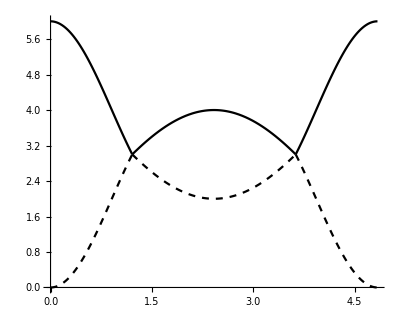

```mathematica
F1a=Plot[F1[JHS,a,kx,Sqrt[3]kx],{kx,0,F},AspectRatio->0.8,PlotTheme->"Monochrome"];
F1b=Plot[F1[JHS,a,2F-kx,Sqrt[3]F],{kx,F,3F},AspectRatio->0.4,PlotTheme->"Monochrome"];
F1c=Plot[F1[JHS,a,kx-4F,-Sqrt[3] (kx-4F)],{kx,3F,4F},AspectRatio->0.8,PlotTheme->"Monochrome"];
F2a=Plot[F2[JHS,a,kx,Sqrt[3]kx],{kx,0,F},AspectRatio->0.8,PlotStyle->Dashed,PlotTheme->"Monochrome"];
F2b=Plot[F2[JHS,a,2F-kx,Sqrt[3]F],{kx,F,3F},AspectRatio->0.4,PlotStyle->Dashed,PlotTheme->"Monochrome"];
F2c=Plot[F2[JHS,a,kx-4F,-Sqrt[3] (kx-4F)],{kx,3F,4F},AspectRatio->0.8,PlotStyle->Dashed,PlotTheme->"Monochrome"];
Show[{F1a,F1b,F1c,F2a,F2b,F2c},PlotRange->All,AxesOrigin->{0,0},GridLines->{{F,2 F,3 F},{0}},PlotTheme->"Monochrome",AspectRatio->753/939]
```

```mathematica
AA stacked bilayer ferromagnet
```

AA bilayer ferromagnet stacked

```mathematica
AF1=Function[{JHS,L,a,kx,ky},JHS((3-2L)+Sqrt[gamsq[a,kx,ky]])];
AF2=Function[{JHS,L,a,kx,ky},JHS((3-2L)-Sqrt[gamsq[a,kx,ky]])];
```

```mathematica
Plot3D[{F1[JHS,a,kx,ky],F2[JHS,a,kx,ky],AF1[JHS,LF,a,kx,ky],AF2[JHS,LF,a,kx,ky]}, {kx, -5,5},{ky,-5,5},AxesLabel->{kx,ky,"E(k)"}]
```

-Graphics3D-

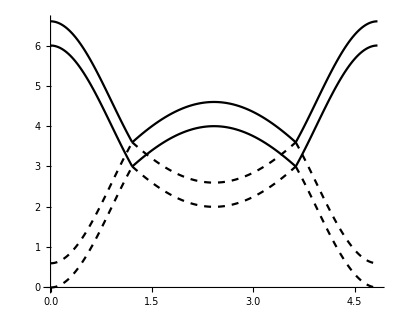

```mathematica
F1a=Plot[F1[JHS,a,kx,Sqrt[3]kx],{kx,0,F},AspectRatio->0.8,PlotTheme->"Monochrome"];
F1b=Plot[F1[JHS,a,2F-kx,Sqrt[3]F],{kx,F,3F},AspectRatio->0.4,PlotTheme->"Monochrome"];
F1c=Plot[F1[JHS,a,kx-4F,-Sqrt[3] (kx-4F)],{kx,3F,4F},AspectRatio->0.8,PlotTheme->"Monochrome"];
F2a=Plot[F2[JHS,a,kx,Sqrt[3]kx],{kx,0,F},AspectRatio->0.8,PlotStyle->Dashed,PlotTheme->"Monochrome"];
F2b=Plot[F2[JHS,a,2F-kx,Sqrt[3]F],{kx,F,3F},AspectRatio->0.4,PlotStyle->Dashed,PlotTheme->"Monochrome"];
F2c=Plot[F2[JHS,a,kx-4F,-Sqrt[3] (kx-4F)],{kx,3F,4F},AspectRatio->0.8,PlotStyle->Dashed,PlotTheme->"Monochrome"];
AF1a=Plot[AF1[JHS,LF,a,kx,Sqrt[3]kx],{kx,0,F},AspectRatio->0.8,PlotTheme->"Monochrome"];
AF1b=Plot[AF1[JHS,LF,a,2F-kx,Sqrt[3]F],{kx,F,3F},AspectRatio->0.4,PlotTheme->"Monochrome"];
AF1c=Plot[AF1[JHS,LF,a,kx-4F,-Sqrt[3] (kx-4F)],{kx,3F,4F},AspectRatio->0.8,PlotTheme->"Monochrome"];
AF2a=Plot[AF2[JHS,LF,a,kx,Sqrt[3]kx],{kx,0,F},AspectRatio->0.8,PlotStyle->Dashed,PlotTheme->"Monochrome"];
AF2b=Plot[AF2[JHS,LF,a,2F-kx,Sqrt[3]F],{kx,F,3F},AspectRatio->0.4,PlotStyle->Dashed,PlotTheme->"Monochrome"];
AF2c=Plot[AF2[JHS,LF,a,kx-4F,-Sqrt[3] (kx-4F)],{kx,3F,4F},AspectRatio->0.8,PlotStyle->Dashed,PlotTheme->"Monochrome"];
Show[{AF1a,AF1b,AF1c,AF2a,AF2b,AF2c,F1a,F1b,F1c,F2a,F2b,F2c},PlotRange->All,AxesOrigin->{0,0},GridLines->{{F,2 F,3 F},{0}},PlotTheme->"Monochrome",AspectRatio->753/939]
```

## AA stacked bilayer antiferromagnet

```mathematica
AE1=Function[{JHS,L,a,kx,ky},JHS*-Sqrt[9+6L+gamsq[a,kx,ky]+2*Sqrt[(3+L)^2*gamsq[a,kx,ky]]]];
AE2=Function[{JHS,L,a,kx,ky},JHS*-Sqrt[9+6L+gamsq[a,kx,ky]-2*Sqrt[(3+L)^2*gamsq[a,kx,ky]]]];
AE3=Function[{JHS,L,a,kx,ky},JHS*Sqrt[9+6L+gamsq[a,kx,ky]+2*Sqrt[(3+L)^2*gamsq[a,kx,ky]]]];
AE4= Function[{JHS,L,a,kx,ky},
JHS*Sqrt[9+6L+gamsq[a,kx,ky]-2*Sqrt[(3+L)^2*gamsq[a,kx,ky]]]];
```

```mathematica
Plot3D[{AE1[JHS,LA,a,kx,ky],AE2[JHS,LA,a,kx,ky],AE3[JHS,LA,a,kx,ky],AE4[JHS,LA,a,kx,ky]},{kx,-5,5},{ky,-5,5}]
```

-Graphics3D-

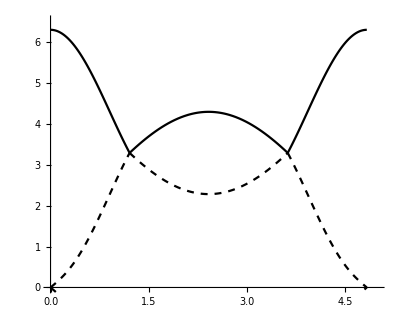

```mathematica
AE1a=Plot[AE1[JHS,LA,a,kx,Sqrt[3]kx],{kx,0,F},AspectRatio->0.8,PlotTheme->"Monochrome"];
AE1b=Plot[AE1[JHS,LA,a,2F-kx,Sqrt[3]F],{kx,F,3F},AspectRatio->0.4,PlotTheme->"Monochrome"];
AE1c=Plot[AE1[JHS,LA,a,kx-4F,-Sqrt[3] (kx-4F)],{kx,3F,4F},AspectRatio->0.8,PlotTheme->"Monochrome"];
AE2a=Plot[AE2[JHS,LA,a,kx,Sqrt[3]kx],{kx,0,F},AspectRatio->0.8,PlotStyle->Dashed,PlotTheme->"Monochrome"];
AE2b=Plot[AE2[JHS,LA,a,2F-kx,Sqrt[3]F],{kx,F,3F},AspectRatio->0.4,PlotStyle->Dashed,PlotTheme->"Monochrome"];
AE2c=Plot[AE2[JHS,LA,a,kx-4F,-Sqrt[3] (kx-4F)],{kx,3F,4F},AspectRatio->0.8,PlotStyle->Dashed,PlotTheme->"Monochrome"];
AE3a=Plot[AE3[JHS,LA,a,kx,Sqrt[3]kx],{kx,0,F},AspectRatio->0.8,PlotTheme->"Monochrome"];
AE3b=Plot[AE3[JHS,LA,a,2F-kx,Sqrt[3]F],{kx,F,3F},AspectRatio->0.4,PlotTheme->"Monochrome"];
AE3c=Plot[AE3[JHS,LA,a,kx-4F,-Sqrt[3] (kx-4F)],{kx,3F,4F},AspectRatio->0.8,PlotTheme->"Monochrome"];
AE4a=Plot[AE4[JHS,LA,a,kx,Sqrt[3]kx],{kx,0,F},AspectRatio->0.8,PlotStyle->Dashed,PlotTheme->"Monochrome"];
AE4b=Plot[AE4[JHS,LA,a,2F-kx,Sqrt[3]F],{kx,F,3F},AspectRatio->0.4,PlotStyle->Dashed,PlotTheme->"Monochrome"];
AE4c=Plot[AE4[JHS,LA,a,kx-4F,-Sqrt[3] (kx-4F)],{kx,3F,4F},AspectRatio->0.8,PlotStyle->Dashed,PlotTheme->"Monochrome"];
Show[{AE1a,AE1b,AE1c,AE2a,AE2b,AE2c,AE3a,AE3b,AE3c,AE4a,AE4b,AE4c},PlotRange->{{0,5},{0,6.5}},AxesOrigin->{0,0},GridLines->{{F,2 F,3 F},{0}},PlotTheme->"Monochrome",AspectRatio->753/939]
```

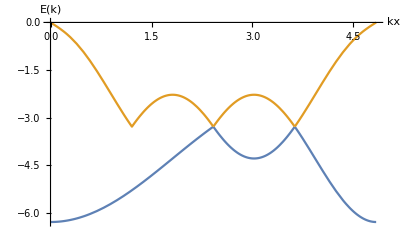

```mathematica
Plot[{LinePlot[AE1[JHS,LA,a,kx1[kx],ky1[kx1[kx]]],AE1[JHS,LA,a,kx2[kx],ky2[kx2[kx]]],AE1[JHS,LA,a,kx3[kx],ky3[kx3[kx]]],0,2*F,3*F,4*F,kx],LinePlot[AE2[JHS,LA,a,kx1[kx],ky2[kx1[kx]]],AE2[JHS,LA,a,kx2[kx],ky2[kx2[kx]]],AE2[JHS,LA,a,kx3[kx],ky3[kx3[kx]]],0,2*F,3*F,4*F,kx]},{kx,0,4*F},GridLines->{{2*F,3*F,4*F},{0}},AxesLabel->{kx,"E(k)"}]
```

## AB Stacked Ferromagnet

```mathematica
BFE1=Function[{JHS,L,a,kx,ky},JHS*(3+Sqrt[gamsq[a,kx,ky]])];
BFE2=Function[{JHS,L,a,kx,ky},JHS*(3-Sqrt[gamsq[a,kx,ky]])];
BFE3=Function[{JHS,L,a,kx,ky},JHS*((3-L)-Sqrt[L^2+gamsq[a,kx,ky]])];
BFE4= Function[{JHS,L,a,kx,ky},JHS*((3-L)+Sqrt[L^2+gamsq[a,kx,ky]])];
Plot3D[{BFE1[JHS,LF,a,kx,ky],BFE2[JHS,LF,a,kx,ky],BFE3[JHS,LF,a,kx,ky],BFE4[JHS,LF,a,kx,ky]},{kx,-5,5},{ky,-5,5}]
```

-Graphics3D-

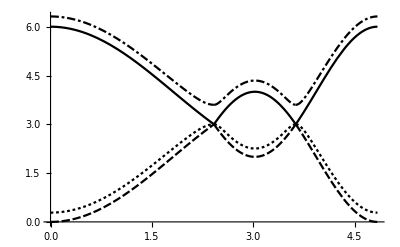

```mathematica
Plot[{LinePlot[BFE1[JHS,LF,a,kx1[kx],ky1[kx1[kx]]],BFE1[JHS,LF,a,kx2[kx],ky2[kx2[kx]]],BFE1[JHS,LF,a,kx3[kx],ky3[kx3[kx]]],0,2*F,3*F,4*F,kx],LinePlot[BFE2[JHS,LF,a,kx1[kx],ky1[kx1[kx]]],BFE2[JHS,LF,a,kx2[kx],ky2[kx2[kx]]],BFE2[JHS,LF,a,kx3[kx],ky3[kx3[kx]]],0,2*F,3*F,4*F,kx],LinePlot[BFE3[JHS,LF,a,kx1[kx],ky1[kx1[kx]]],BFE3[JHS,LF,a,kx2[kx],ky2[kx2[kx]]],BFE3[JHS,LF,a,kx3[kx],ky3[kx3[kx]]],0,2*F,3*F,4*F,kx],LinePlot[BFE4[JHS,LF,a,kx1[kx],ky1[kx1[kx]]],BFE4[JHS,LF,a,kx2[kx],ky2[kx2[kx]]],BFE4[JHS,LF,a,kx3[kx],ky3[kx3[kx]]],0,2*F,3*F,4*F,kx]},{kx,0,4*F},GridLines->{{2*F,3*F,4*F},{0}},PlotTheme->"Monochrome"]
```

## AB stacked bilayer antiferromagnet

```mathematica
BAE1=Function[{JHS,L,a,kx,ky},JHS*Sqrt[9+3*L+gamsq[a,kx,ky]+Sqrt[3]*Sqrt[3*L^2+12*gamsq[a,kx,ky]+4*L*gamsq[a,kx,ky]]]];
BAE2=Function[{JHS,L,a,kx,ky},JHS*Sqrt[9+3*L+gamsq[a,kx,ky]-Sqrt[3]*Sqrt[3*L^2+12*gamsq[a,kx,ky]+4*L*gamsq[a,kx,ky]]]];
BAE3=Function[{JHS,L,a,kx,ky},-JHS*Sqrt[9+3*L+gamsq[a,kx,ky]+Sqrt[3]*Sqrt[3*L^2+12*gamsq[a,kx,ky]+4*L*gamsq[a,kx,ky]]]];
BAE4=Function[{JHS,L,a,kx,ky},-JHS*Sqrt[9+3*L+gamsq[a,kx,ky]-Sqrt[3]*Sqrt[3*L^2+12*gamsq[a,kx,ky]+4*L*gamsq[a,kx,ky]]]];
Plot3D[{BAE1[JHS,LA,a,kx,ky],BAE2[JHS,LA,a,kx,ky]},{kx,-5,5},{ky,-5,5}]
```

-Graphics3D-

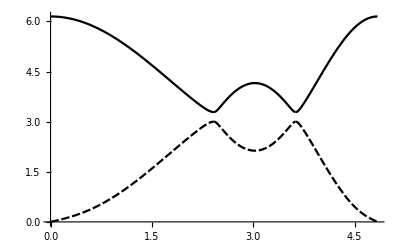

```mathematica
Plot[{LinePlot[BAE1[JHS,LA,a,kx1[kx],ky1[kx1[kx]]],BAE1[JHS,LA,a,kx2[kx],ky2[kx2[kx]]],BAE1[JHS,LA,a,kx3[kx],ky3[kx3[kx]]],0,2*F,3*F,4*F,kx],LinePlot[BAE2[JHS,LA,a,kx1[kx],ky1[kx1[kx]]],BAE2[JHS,LA,a,kx2[kx],ky2[kx2[kx]]],BAE2[JHS,LA,a,kx3[kx],ky3[kx3[kx]]],0,2*F,3*F,4*F,kx]},{kx,0,4*F},GridLines->{{2*F,3*F,4*F},{0}},PlotTheme->"Monochrome",BaseStyle->24]
```

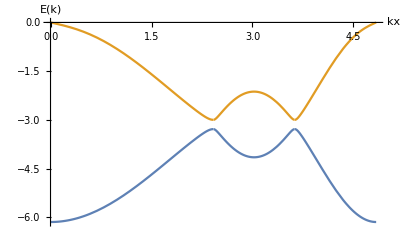

```mathematica
Plot[{LinePlot[BAE3[JHS,LA,a,kx1[kx],ky1[kx1[kx]]],BAE3[JHS,LA,a,kx2[kx],ky2[kx2[kx]]],BAE3[JHS,LA,a,kx3[kx],ky3[kx3[kx]]],0,2*F,3*F,4*F,kx],LinePlot[BAE4[JHS,LA,a,kx1[kx],ky1[kx1[kx]]],BAE4[JHS,LA,a,kx2[kx],ky2[kx2[kx]]],BAE4[JHS,LA,a,kx3[kx],ky3[kx3[kx]]],0,2*F,3*F,4*F,kx]},{kx,0,4*F},GridLines->{{2*F,3*F,4*F},{0}},AxesLabel->{kx,"E(k)"}]
```